```mathematica
CloseKernels[]
```

{KernelObject[5,local,<defunct>],KernelObject[6,local,<defunct>],KernelObject[7,local,<defunct>],KernelObject[8,local,<defunct>]}

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
e=1;
m=6;
P=2^m;
Ep=100;
Dynamic[{Ep,e,t}]
```

```mathematica
ParallelTable[(Label[New];
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
T=1280-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=300;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
c=Table[10*Price⟦1⟧,{i,1,n}];
NStock=Table[0,{i,1,n},{i,1,2}];
W=Table[10*Price⟦1⟧,{i,1,n}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
"initial set";
AgentStrategy=Table[RandomChoice[{1,-1}],{n},{S},{P}];
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,
Do[W⟦i⟧=10*Price⟦1⟧,{i,1,n}];
Do[c⟦i⟧=10*Price⟦1⟧,{i,1,n}];
Do[NStock⟦i,2⟧=0,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
];
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Goto[sample],Goto[begin]];
Label[sample];
{Price⟦T⟧-Price⟦1⟧,Total[c⟦3;;n⟧-3000],NStock⟦All,2⟧,NStock⟦All,2⟧*Price⟦T⟧}),{e,1,Ep}]//AbsoluteTiming
```

```mathematica
aaaa=%⟦2⟧
```

```mathematica
N[{Abs[aaaa⟦1,1⟧],aaaa⟦1,2⟧}]
```

{56.7171,268.504}

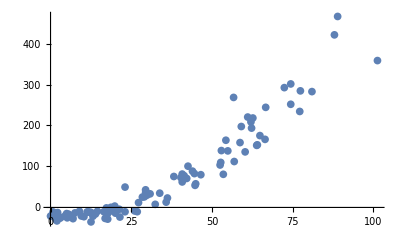

```mathematica
ListPlot[N[Table[{Abs[aaaa⟦i,1⟧],aaaa⟦i,2⟧},{i,1,Length[aaaa⟦All,1⟧]}]]]
```

```mathematica
N[{{aaaa⟦1,1⟧,aaaa⟦1,2⟧},{aaaa⟦6,1⟧,aaaa⟦6,2⟧},{aaaa⟦7,1⟧,aaaa⟦7,2⟧}}]
```

{{284.676,-0.116497},{380.996,0.640344},{197.312,-0.809226}}

```mathematica
Export["C:\\Users\\Jack\\Desktop\\LabWork\\final\\Price168.txt",Compress[{aaaa⟦1,3⟧,aaaa⟦6,3⟧,aaaa⟦7,3⟧}]]
```

C:\Users\Jack\Desktop\LabWork\final\Price168.txt

```mathematica
Export["C:\\Users\\Jack\\Desktop\\LabWork\\final\\PTAT.txt",Compress[{{aaaa⟦1,1⟧,aaaa⟦1,2⟧},{aaaa⟦6,1⟧,aaaa⟦6,2⟧},{aaaa⟦7,1⟧,aaaa⟦7,2⟧}}]]
```

C:\Users\Jack\Desktop\LabWork\final\PTAT.txt

```mathematica
WA=Uncompress[ReadList["C:\\Users\\Jack\\Desktop\\LabWork\\final\\m2s2T399p10 2.txt",String]⟦1⟧]
```

{{100+827/(√101),100-113/(√101)-8 √101,1/99 (9900+11584/(√101)-1063 √101)},{100+34/(√101)-5 √101,100-374/(√101)-19 √101,1/99 (9900-7710/(√101)-829 √101)},996,{100+65/(√101)+4 √101,100+6029/(√101)+78 √101,1/99 (9900-23345/(√101)-690 √101)},{100-213/(√101)-2 √101,100-823/(√101)-16 √101,1/99 (9900-12993/(√101)-766 √101)}}
 |  |  |  |

```mathematica
N[WA⟦All,3⟧];
Ep=1000;
WAM=Mean[N[WA⟦All,3⟧-100,3]]
WAσ=StandardDeviation[N[WA⟦All,3⟧-100,4]]
WAP=1/Ep Total[UnitStep[N[WA⟦All,3⟧-100]]]
```

-85.9

19.2

0

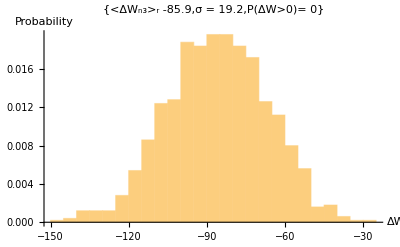

```mathematica
Histogram[N[WA⟦All,3⟧]-100,{5},PDF,AxesLabel->{ΔW,Probability},PlotLabel->{ "<ΔW_n3>_r "<>ToString[WAM],"σ = "<>ToString[WAσ],"P(ΔW>0)= "<>ToString[WAP]},LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```

```mathematica
N[WA⟦All,3⟧];
Ep=1000;
WAM=Mean[N[WA⟦All,1⟧-100,3]]
WAσ=StandardDeviation[N[WA⟦All,1⟧-100,4]]
WAP=N[1/Ep Total[UnitStep[N[WA⟦All,1⟧-100]]]]
```

7.3

39.9

0.577

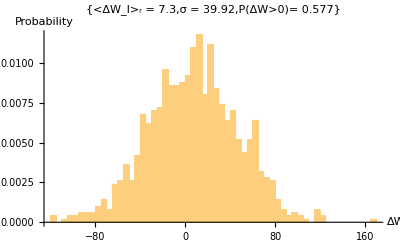

```mathematica
Histogram[N[WA⟦All,1⟧]-100,{5},PDF,AxesLabel->{"ΔW",Probability},PlotLabel->{ "<ΔW_I>_r = "<>ToString[WAM],"σ = "<>ToString[WAσ],"P(ΔW>0)= "<>ToString[WAP]},LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```

```mathematica
Ⅱ
```

```mathematica
N[WA⟦All,3⟧];
Ep=1000;
WAM=Mean[N[WA⟦All,2⟧-100,4]]
WAσ=StandardDeviation[N[WA⟦All,2⟧-100,4]]
WAP=N[1/Ep Total[UnitStep[N[WA⟦All,2⟧-100]]]]
```

-83.3

434.

0.39

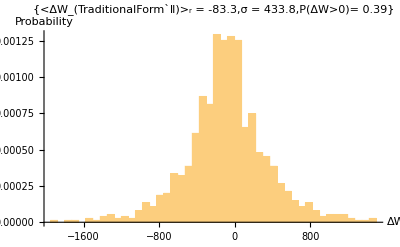

```mathematica
Histogram[N[WA⟦All,2⟧]-100,{75},PDF,AxesLabel->{"ΔW",Probability},PlotLabel->{ "<ΔW_(TraditionalForm`:2161)>_r = "<>ToString[WAM],"σ = "<>ToString[WAσ],"P(ΔW>0)= "<>ToString[WAP]},LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```

```mathematica
WA=Uncompress[ReadList["C:\\Users\\Jack\\Desktop\\LabWork\\final\\openm4s2T1999EP1000final.txt",String]⟦1⟧]
```

{{100+197/(√101)+2 √101,100+180/(√101)-15 √101-61 (203/(√101)-2 √101)-50 (-118/(√101)+√101)-57 (-94/(√101)+√101),1/101 (10100+127817/(√101)-3256 √101-102 (203/(√101)-2 √101)+24 (-118/(√101)+√101)+88 (-94/(√101)+√101))},{100+42/(√101)-3 √101,100-5016/(√101)+39 √101,1/101 (10100-227011/(√101)+410 √101)},997,{100-17/(√101),100+1273/(√101)-22 √101,1/101 (10100-231864/(√101)+935 √101)}}
 |  |  |  |

```mathematica
Ep=1000;
WAM=Mean[N[WA⟦All,1⟧-100,3]]
WAσ=StandardDeviation[N[WA⟦All,1⟧-100,4]]
WAP=N[1/Ep Total[UnitStep[N[WA⟦All,1⟧-100]]]]
```

8.2

40.7

0.583

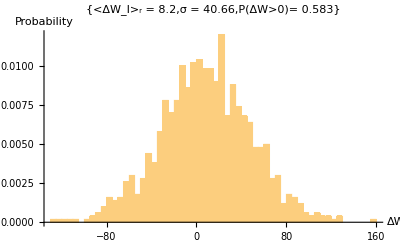

```mathematica
Histogram[N[WA⟦All,1⟧]-100,{5},PDF,AxesLabel->{"ΔW",Probability},PlotLabel->{ "<ΔW_I>_r = "<>ToString[WAM],"σ = "<>ToString[WAσ],"P(ΔW>0)= "<>ToString[WAP]},LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```

```mathematica
Ep=1000;
WAM=Mean[N[WA⟦All,2⟧-100,4]]
WAσ=StandardDeviation[N[WA⟦All,2⟧-100,4]]
WAP=N[1/Ep Total[UnitStep[N[WA⟦All,2⟧-100]]]]
```

-182.

1200.

0.391

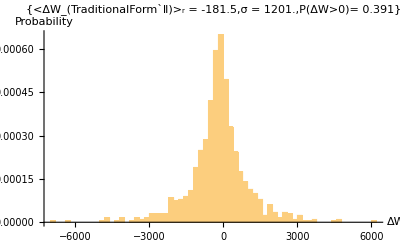

```mathematica
Histogram[N[WA⟦All,2⟧]-100,{200},PDF,AxesLabel->{"ΔW",Probability},PlotLabel->{ "<ΔW_(TraditionalForm`:2161)>_r = "<>ToString[WAM],"σ = "<>ToString[WAσ],"P(ΔW>0)= "<>ToString[WAP]},LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```

```mathematica
ReadList["C:\\Users\\Jack\\Desktop\\LabWork\\final\\closem4s2T1999Ep1000final.txt",String]⟦1⟧;
```

```mathematica
WA={{144.5776661214075, 969.8615116815727}, {161.79180951204032, 191.54342149931898}, {159.70223141259936, 306.1717058115098}, {71.24342520293132, 109.95037190209979}, {104.67667479398695, -455.8277744512999}, {238.11116200114648, -55.7233202678633}, {84.97493842782916, -14.827291750232746}, {163.8813876114813, 448.5615277305592}, {227.86227894198362, -560.5056868613908}, {143.7816363692395, 1349.4681997466837}, {170.7471442239302, 1308.27366007199}, {82.38784173328318, 608.4640041973045}, {213.73275084100175, -246.0739347550342}, {178.60793802658912, -403.38931452723347}, {202.19031943456588, 1562.1076472945579}, {134.6272942193076, 170.74714422393023}, {148.65731860126846, -3027.998911144122}, {207.26500910463682, 543.5875793956131}, {190.15036943302502, 240.30024381960848}, {148.25930372518448, -413.3396864293339}, {142.38858430294553, 574.632739730165}, {20.69553594026388, 55.4223338785925}, {172.2397000092452, 53.03424462208852}, {201.0957785253349, 2492.3679164218765}, {77.71116693929625, -1188.175146445852}, {105.07468967007094, 1683.9001993762606}, {186.17022067218505, 1399.1205555381619}, {13.133253294667977, -1711.4652047772847}, {151.44342273385644, 651.9471294094809}, {153.53300083329742, 219.6034702632407}, {201.6928008394609, -2114.952785407436}, {120.69677355636776, -1282.2061609206962}, {19.401987592990878, 253.83274960646432}, {102.38808925650397, -951.9533174900007}, {101.39305206629398, 280.49974630409207}, {184.57816116784906, 1112.947859633769}, {188.95632480477303, 326.27145705375153}, {169.35409215763625, -834.2404178881588}, {270.2508632449292, -282.59179963574087}, {181.29453844015612, -970.8590241039905}, {168.75706984351024, 2781.8242350539626}, {94.62679917286606, 44.27791734824071}, {96.91538471034903, -96.61934878549386}, {166.66749174406925, 2369.082808554859}, {144.47816240238652, 754.1374488440466}, {93.13424338755108, 7.26253387242906}, {142.09007314588254, 41.98933181075765}, {70.04938057467933, 78.60670041048522}, {52.536726026983516, -98.31091200885083}, {117.6121582667168, -295.52728310847056}, {54.6263041264245, 789.2622616584592}, {172.1401962902242, 888.4674695223954}, {233.93200580226454, 2285.201173420157}, {115.02506157217083, 191.2449103422565}, {220.8970186105137, 336.1223252368303}, {109.4528533069949, 78.90521156754824}, {133.23424215301364, -1036.3324712198078}, {150.24937810560445, 106.06972686028121}, {10.446652881100981, 156.31910496588537}, {237.4146359679995, 58.8054603253064}, {254.8277867966743, -338.11487484945815}, {307.4652541587827, 2545.104887503006}, {151.14491157679345, -195.92406036845077}, {109.95037190209989, 615.3297608097535}, {197.71265207862092, 946.5776414306588}, {129.0550859541317, 7409.642703001601}, {120.89578099440978, -2136.3460849969506}, {150.94590413875147, -324.8808802196652}, {170.05061819078324, -250.25309095391617}, {65.77072065677638, 472.64142773364097}, {131.74168636769866, 738.0178463626451}, {7.859556186555011, 1061.5044368999124}, {61.890075614957425, 409.65557359334866}, {236.61860621583153, 682.196259991865}, {112.63697231566685, -4912.698853120862}, {76.61662603006525, 152.83647480015043}, {187.66277645750006, 1010.956547637245}, {19.202980154948886, 2086.0942316591386}, {83.48238264251418, 541.0999864200882}, {100., -25.47418968547963}, {249.05657109345634, 1878.5294737813347}, {83.48238264251418, 233.63349464520155}, {145.3736958735755, 797.0235517420974}, {192.737466127571, -181.89403598648994}, {85.27344958489215, -801.5036943302503}, {139.90099132742057, -1143.6969840434654}, {131.54267892965663, -498.51486991130855}, {160.00074256966235, -772.6476158141606}, {210.4491281133088, -772.1500972190555}, {151.84143760994044, 694.3357137124265}, {113.33349834881386, -1669.7731465074867}, {179.10545662169412, 80.69627850992612}, {5.869481806135028, -1038.9195679143536}, {27.16327767662876, -1332.8535539023849}, {49.45211073733256, 184.87667232491208}, {86.06947933706016, -159.50569920676517}, {344.18212647753137, -312.54241906106154}, {117.01513595259081, -355.528025678133}, {93.23374710657208, 1125.584831949436}, {192.140443813445, 88.45756859356439}, {109.4528533069949, -551.351344711459}, {182.58808678742912, -233.23795500132536}, {272.83795993947507, 394.3320008641148}, {115.82109132433882, 351.6449054041062}, {197.41414092155793, -939.8138637694387}, {148.85632603931046, 695.9277732167625}, {75.02456652572928, 327.5650054010246}, {267.06674423625714, 2239.329958951477}, {246.56897811793138, 715.6295095829203}, {49.452110737332546, 481.8952736025939}, {135.4233239714756, -244.78038640776128}, {145.9707181877015, 911.9503472113512}, {149.35384463441545, 149.15483719637342}, {141.69205826979854, 3080.2358883979387}, {197.01612604547392, 2631.5736193322546}, {76.81563346810725, -622.3970000924522}, {191.54342149931898, 646.7729360203891}, {223.88213018114365, 769.6600290113228}, {159.70223141259936, 391.94391160761074}, {42.58635412488363, -981.2074108821741}, {223.38461158603866, 1634.3473473038039}, {120.79627727538877, 137.21439091385363}, {189.45384339987802, -1980.6227647290873}, {188.75731736673103, 406.7699657417397}, {88.75607975062712, 110.94540909230983}, {304.8781574642368, -2585.0083540626347}, {138.2094281040636, 771.8491108297848}, {262.98709175639624, 334.72927317053643}, {73.73101817845628, -1611.36446344216}, {266.17121076506817, 34.32754544614072}, {137.81141322797959, -307.6667368290325}, {209.95160951820378, -436.92206783730995}, {220.6980111724717, 1436.2354427329942}, {203.68287521988088, -459.0118934599719}, {291.1466442393389, 1725.791265084101}, {151.94094132896143, 631.6483707291973}, {176.51835992714817, 1171.2570389800744}, {92.83573223048808, 922.7962525846401}, {224.97667109037462, 703.9875744574636}, {70.54689916978433, -1573.8515613712439}, {124.17940372210273, -1013.6456232830197}, {159.40372025553634, 5289.516961821177}, {228.2602938180676, -211.14812937866358}, {206.96649794757383, -434.83248973786925}, {80.09925619580022, 714.8334798307521}, {121.39329958951475, 1520.7141001818225}, {95.12431776797105, -915.733963766357}, {110.84590537328889, -221.09850128076343}, {192.438954970508, -251.54663930118932}, {46.66600660474458, 617.4193389091944}, {56.11885991173948, 1208.7699410509908}, {158.11017190826334, 531.2491182370093}, {182.88659794449208, -288.36301533895875}, {89.25359834573212, -52.34019382114934}, {109.0548384309109, -485.67889015759965}, {132.73672355790865, -1055.2381778337974}, {130.24913058238366, -1168.771921236757}, {160.10024628868334, 829.262756704901}, {193.73250331778098, -4.677912410090855}, {81.19379710503121, -1283.4997092679687}, {167.56302521525828, 318.8086781271767}, {187.56327273847904, -416.8223165950684}, {106.16923057930192, -116.71910002773566}, {131.54267892965663, 526.5724434430223}, {54.228289250340495, -659.8103984443477}, {175.52332273693816, -744.4880633312177}, {138.30893182308458, 570.5530872503039}, {110.14937934014189, -131.94316903794845}, {172.9362260423922, 1891.9624758491696}, {140.89602851763055, 2064.8999395076653}, {188.16029505260502, -107.06723928269878}, {216.02133637848473, -1708.579596925676}, {142.28908058392454, 382.39155458159496}, {152.63746736210842, 915.5324810961072}, {167.06550662015326, 505.4776550105705}, {134.6272942193076, 205.77245331932184}, {174.6277892657492, -294.4327421992398}, {-3.284860343796879, -642.7952624917568}, {92.83573223048808, -2753.667157803228}, {160.49826116476734, -643.7902996819669}, {88.55707231258512, 32.337471065720706}, {302.5895719267538, -3627.1108033695564}, {31.839952470615742, 455.62629178105004}, {0.6952884170430877, 3150.2865065887217}, {127.0650115737117, 489.2585488101478}, {162.38883182616632, -1468.8751378040897}, {204.57840869106985, -394.1354686582806}, {126.3684855405647, -302.0945285638566}, {165.6724545538593, -264.482122773919}, {164.7769210826703, -1971.6674300171974}, {232.14093885988652, 1056.3302435108208}, {125.07493719329173, 1541.908392333295}, {279.20619795681904, -483.8878232152216}, {156.02059380882238, 354.63001697473624}, {101.69156322335697, 46.86501404278653}, {181.9910644733031, -5.075927286174874}, {112.63697231566687, -33.93200580226443}, {170.7471442239302, 177.31438967931615}, {69.94987685565833, -251.34763186314717}, {221.59354464366066, 1295.9351989133859}, {140.89602851763055, -524.7838517328522}, {167.06550662015326, 287.166495478499}, {75.52208512083428, -168.95855251376008}, {128.4580636400057, -281.09924385042586}, {99.60198512391601, 104.57717107496597}, {33.13350081788874, 865.4821104285445}, {166.96600290113227, 59.00446776334843}, {-68.85781117863515, -2670.979567296778}, {108.4578161167849, 1840.9170679913968}, {148.45831116322648, -1313.4503286932904}, {59.80049751551644, 82.1888342952412}, {141.89106570784054, 433.2379550013253}, {112.73647603468787, -423.8870806455592}, {53.929778093277505, -39.80272522450346}, {32.43697478474174, 2601.2249850308503}, {73.43250702139329, 1003.8917835867546}, {203.98138637694387, 1396.035940248511}, {111.64193512545688, 600.7027141136666}, {228.9568198512146, 243.7828739853431}, {135.12481281441262, -2975.858962377118}, {139.10496157525256, 300.0024752322078}, {172.9362260423922, 933.3436468008658}, {80.49727107188423, 2187.7870324985984}, {97.21389586741203, 3447.8026264615087}, {84.67642727076617, 623.8870806455593}, {112.93548347272989, -201.5957723526477}, {89.1540946267111, 5.670474368092982}, {143.38362149315554, 156.51811240392738}, {106.26873429832293, -1024.2925212182668}, {315.32604796144165, 1351.6572815651455}, {150.94590413875144, -379.70742940023575}, {190.64788802813, 2798.739867287533}, {111.44292768741488, 704.7836042096314}, {233.03647233107554, 598.7126397332466}, {162.38883182616632, 369.45607110886505}, {68.65632850838534, 3.0833776735470337}, {115.92059504335982, -391.6478756827555}, {103.88064504181895, -1746.9880324677824}, {78.40769297244321, -264.88013765000323}, {236.8176136538735, 342.1920520971114}, {83.97990123761922, -2091.4699077184796}, {105.77121570321793, -282.6913033547619}, {104.17915619888196, -373.3391913828917}, {208.75756488995182, -65.07666985583717}, {228.1607900990466, -19.404462825198692}, {200.0012376161039, 1590.5657109345639}, {148.06029628714248, 1225.5860695655397}, {150.54788926266744, -148.7592975524973}, {171.6426776951192, -376.92132526764783}, {103.28362272769297, -555.6300046293618}, {167.76203265330025, -1318.6245220823814}, {71.3429289219523, -99.60446035612387}, {130.44813802042566, 36.815138421665694}, {106.66674917440693, -439.60866825087714}, {133.33374587203463, 284.28088762689003}, {200.2997487731669, -18.80744051107274}, {177.61290083637914, -120.1022264744496}, {67.26327644209138, 515.9255455077754}, {194.130518193865, -759.5131249033888}, {52.33771858894153, -1408.4763803583435}, {165.4734471158173, -824.887068300185}, {137.41339835189558, 315.92307027556774}, {202.2898231535869, -11.941683898623864}, {155.4235714946964, -20.200492577366845}, {145.87121446868048, -134.92828060857843}, {167.36401777721625, 1691.5619857408776}, {59.20347520139045, -136.81885126997736}, {157.81166075120035, 636.9220678373101}, {158.11017190826337, -551.7493595875429}, {117.5126545476958, 175.32431529889618}, {72.5369735502043, 719.6096583437603}, {108.05980124070092, -916.9280083946089}, {1.2923107311690814, 1500.6143489395809}, {80.09925619580022, -190.25234838425376}, {68.85533594642735, 17.909431807676015}, {99.203970247832, -1597.3344390601997}, {26.06873676739781, 2877.347805314122}, {94.02977685874006, 351.3463942470432}, {170.0506181907832, 83.48238264251401}, {58.00943057313846, 1770.1699237674666}, {151.44342273385644, 635.8275269280791}, {151.74193389091943, 178.70744174561025}, {173.4337446374972, -1659.2257522912605}, {139.1049615752526, 83.18387148545116}, {119.2042177710528, 628.0662368444418}, {233.43448720715955, 673.0419178419327}, {175.92133761302216, -1200.2150964473929}, {197.91165951666295, -896.4302422762831}, {90.04962809790011, 236.02158390170553}, {38.30769420698067, 1186.9786265853922}, {65.57171321873439, -75.22604919597927}, {139.90099132742057, 34.52655288418276}, {206.26997191442683, 791.1528323198584}, {98.50744421468502, -572.6451405819525}, {169.05558100057326, 1782.7073923641128}, {71.44243264097331, -1189.4686947931248}, {228.3597975370886, 8.257571062639045}, {45.471961976492594, 329.25656862438154}, {142.88610289805052, -1107.9751489149269}, {127.16451529273272, -79.00719051877708}, {210.1506169562458, 854.2381901791719}, {135.12481281441262, 148.75682232028947}, {80.79578222894722, -8.658061170930814}, {200.8967710872929, -244.38237153167725}, {110.94540909230987, 333.2367173852214}, {80.29826363384223, 34.42704916516172}, {59.30297892041145, -340.0054455108572}, {159.00570537945237, -749.2642418442258}, {217.6133958828207, -1774.7495700746404}, {84.37791611370317, 245.17592605163733}, {262.2905657232492, 1059.8128736765555}, {151.54292645287742, -549.3612703310388}, {161.29429091693532, 193.6329995987603}, {125.77146322643873, 2113.358250670892}, {122.08982562266175, 160.89627604085138}, {158.40868306532636, -94.43026696703191}, {111.44292768741487, -727.5724310976481}, {257.61389092926225, 526.3734360049804}, {170.54813678588823, 52.93474090306751}, {168.16004752938426, 1230.0637369214846}, {192.737466127571, -286.17393352049675}, {162.68734298322929, 260.3004913428291}, {186.17022067218505, 715.8285170209624}, {154.8265491805704, -214.0337372302725}, {123.58238140797674, -453.53918891381704}, {156.4186086849064, -877.0270170671876}, {164.3789062065863, 133.93076818616063}, {209.7526020801618, 417.71537483404956}, {152.33895620504543, 1035.2354550783687}, {119.60223264713679, -727.174416221564}, {123.58238140797674, 2.1878442023580646}, {308.0622764729087, -320.5027165827414}, {86.16898305608116, -19.802477701282672}, {190.24987315204604, 123.58238140797653}, {151.94094132896143, 498.2138835220377}, {213.03622480785475, -865.8826005368364}, {202.78734174869186, -372.44365791170276}, {132.63721983888763, 580.6029628714248}, {307.6642615968247, 5849.324885033317}, {10.944171476205973, 161.79180951204017}, {77.31315206321227, -126.07244961570952}, {-39.90222894352445, 1651.0639720993308}, {96.81588099132803, -149.55532730466348}, {85.07444214685016, 499.20892071224785}, {150.64739298168843, 283.18634671765903}, {53.43225949817251, 773.2421628960785}, {27.262781395649796, 1197.3270133635765}, {121.09478843245176, -17.314884725757715}, {148.55781488224744, 862.2979914198725}, {169.45359587665723, -131.8436653189275}, {215.62332150240073, -302.4925434399406}, {152.63746736210842, 1570.167448535259}, {140.89602851763055, 2243.409611431338}, {242.98684423317542, -572.6451405819527}, {248.95706737443538, 297.8133934137458}, {212.33969877470778, 291.04714052031795}, {46.56650288572358, 127.6620338878377}, {90.84565785006811, -111.94292151472769}, {160.19975000770432, -1068.8701873396744}, {171.0456553809932, 645.1808765160536}, {155.9210900898014, -169.157559951802}, {135.12481281441262, 227.66327150394162}, {132.83622727692963, -27.862278941983597}, {150.74689670070944, 115.72158760531781}, {127.8610413258797, 232.14093885988657}, {159.70223141259936, -961.7046819540584}, {249.35508225051936, 1877.9324514672085}, {170.15012190980423, 855.929753402529}, {42.08883552977863, 645.379883954095}, {84.37791611370318, 366.66996697627707}, {216.71786241163173, 304.7786537452157}, {192.040940094424, 90.44764297398414}, {126.56749297860671, -40.99676985275545}, {238.1111620011465, -180.69999135823798}, {148.85632603931043, -355.9260405542173}, {57.113897101949476, 401.5957723526477}, {157.71215703217936, -1337.7292361344134}, {253.9322533254853, -4319.955198912772}, {159.60272769357834, 114.12952810098182}, {175.02580414183316, 84.77593098978711}, {183.98113885372308, 451.24812814412616}, {172.5382111663082, 115.72158760531784}, {174.5282855467282, 88.05955371748013}, {233.53399092618054, 97.71141446251704}, {183.1851091015551, -956.9285034410502}, {127.6620338878377, -3428.7998913607057}, {143.8811400882605, 465.47715996412904}, {150.05037066756245, -125.37592358256249}, {200.6977636492509, 2206.792242831611}, {163.3838690163763, -105.57468349738375}, {13.332260732709955, 76.91513718712824}, {168.25955124840527, -469.45978395717674}, {159.00570537945237, 305.87319465444676}, {145.1746884355335, 435.82505169587137}, {35.82010123145571, -851.2555538407496}, {180.10049381190413, -70.84788555905513}, {241.09627357177646, 0.09826610291710836}, {127.96054504490067, 510.95035955672546}, {219.50396654421968, 684.1863343722846}, {376.222324002293, 847.2729298477019}, {214.42927687414874, -2183.510847812904}, {95.42282892503405, 654.633729823048}, {163.7818838924603, 703.8880707384424}, {157.51314959413736, -272.5419240146199}, {169.95111447176222, -52.04168266408669}, {71.54193635999431, 408.85954384118065}, {-23.583619024080647, -1033.1483522111355}, {162.2893281071453, 933.244143081845}, {177.41389339833717, -116.12207771360966}, {134.03027190518162, 66.96476528502751}, {39.89975371131666, 98.70645165272701}, {237.1161248109365, 51.04417024166855}, {98.60694793370601, -81.59428721332301}, {177.01587852225316, -149.0578087095605}, {189.05582852379402, 189.25483596183602}, {30.048885528237776, 2955.557728464627}, {181.49354587819812, 519.0101607974265}, {135.52282769049663, 57.21340082097046}, {204.18039381498585, -461.4994864354969}, {174.72729298477017, -152.34143143725325}, {-4.777416129111856, 820.1084145549692}, {272.7384562204541, 2099.7262411650154}, {96.51736983426504, 1292.5520724666721}, {209.7526020801618, -17.712899601841713}, {184.18014629176508, -1481.1140952436726}, {276.02207894814705, -333.73671121253426}, {98.90545909076901, 1548.0776229125972}, {103.88064504181895, 1549.669682416933}, {110.94540909230989, 361.39626986816415}, {125.87096694545971, -108.0622764729085}, {117.11463967161181, -56.02183142492629}, {115.32357272923383, 2900.8306830030774}, {79.90024875775822, -541.1024616522959}, {108.55731983580591, 1963.0081312301625}, {198.40917811176791, 731.2515934692171}, {149.75185951049946, 5.968985525156029}, {149.85136322952044, 514.6319971605024}, {156.12009752784337, -66.76823307919418}, {166.66749174406928, -421.29998395101325}, {222.68808555289166, 768.5654881020916}, {151.84143760994044, 1965.0977093296037}, {197.41414092155793, 2126.890756457748}, {237.7131471250625, -1346.883578284345}, {29.35235949509078, -214.13324094929362}, {229.55384216534057, 633.5389413905962}, {169.55309959567825, -451.64861825241815}, {116.41811363846482, -1526.0897762411644}, {103.88064504181895, -2740.134652016372}, {219.4044628251987, 3113.768641708015}, {98.80595537174801, -411.15060461087137}, {134.6272942193076, -675.3329786116237}, {156.9161272800114, 829.063749266859}, {97.31339958643304, -191.3468892934848}, {249.15607481247739, 446.5714533501392}, {128.1595524829427, -292.24366038077767}, {117.41315082867482, 611.0511008918504}, {152.23945248602445, 1449.7679485198505}, {272.7384562204541, -1491.8604968979405}, {180.39900496896712, 135.22431653343352}, {53.7307706552355, 1274.9399141999552}, {143.58262893119752, -803.4937687106701}, {121.49280330853577, -790.5582852379404}, {134.12977562420264, -176.32182772131398}, {114.12952810098184, -325.6769099718333}, {155.1250603376334, 1780.6178142646713}, {198.01116323568394, 245.0764223326164}, {30.844915280405758, 348.0627715193503}, {149.65235579147844, -905.1865695501306}, {195.324562822117, -253.1386988055259}, {112.73647603468785, 133.33374587203468}, {317.11711490381964, -1929.9753717473986}, {73.5320107404143, 219.50396654421968}, {186.76724298631106, -1095.7361914753446}, {228.6583086941516, -575.4312447145406}, {77.91017437733824, -137.3163698650824}, {148.95582975833145, 467.5667380635699}, {118.80620289496879, 1428.3746489303353}, {122.58734421776676, 376.62033887837697}, {123.58238140797674, -2460.230690410302}, {71.54193635999431, 3617.9539859874167}, {4.97394833494603, -26.369723156668613}, {142.6870954600085, 515.0300120365864}, {123.38337396993475, 3663.029170703929}, {177.51339711735815, 279.90272398996603}, {160.10024628868334, 2143.308870096213}, {106.96526033146992, 1525.5897824138515}, {123.88089256503974, -629.660771580985}, {170.54813678588823, -475.2309996603947}, {110.34838677818388, 353.9334909415893}, {145.9707181877015, -528.4654893366292}, {75.22357396377127, 545.2791426189701}, {48.059058671038564, 223.08610042897564}, {79.40273016265323, 186.86674670533205}, {111.64193512545687, 259.2059504335983}, {270.6488781210131, -968.4709348474863}, {113.33349834881386, 980.9064244929037}, {2.7848665164840583, 5174.689670070944}, {139.30396901329456, 1543.3014443995892}, {142.7865991790295, 408.9590475602016}, {213.03622480785475, 228.75781241317262}, {79.90024875775823, 238.80768803429336}, {138.30893182308458, 537.915867411416}, {252.24069010212833, -163.98336656271044}, {69.35285454153234, 155.02555661861243}, {149.15483719637348, 307.56475787780374}, {86.36799049412315, -453.53918891381693}, {161.1947871979143, 95.52233264405504}, {162.18982438812432, -79.20619795681904}, {149.05533347735246, 97.810918181538}, {144.9756809974915, -1051.1585253539365}, {166.86649918211128, -300.2039579024576}, {171.74218141414022, 849.7605228232267}, {219.50396654421965, -1307.181594394966}, {88.65657603160612, -1142.0054208201086}, {104.87568223202894, 1496.5346964597206}, {153.53300083329742, -267.069219468465}, {52.43722230796252, -70.54937440199205}, {0.1977698219380919, -384.38410419422274}, {8.257571062639002, -676.2285120828126}, {215.22530662631672, 3455.3649091071047}, {68.15880991328035, 440.7007339279003}, {39.700746273274675, -4084.230888552024}, {39.501738835232665, -54.82778679667436}, {235.22555414953752, 1198.322050553786}, {100.29851115706302, -2199.9289614513687}, {103.08461528965097, 164.9759285207124}, {171.34416653805621, -191.64540045054784}, {62.9846165241884, -74.82803431989508}, {121.39329958951477, 361.1972624301221}, {91.94019875929908, -1483.701191938219}, {178.50843430756814, 198.80719298785192}, {160.19975000770432, 1548.8736526647651}, {118.01017314280081, 74.7260553686663}, {165.2744396777753, 33.432011974951735}, {82.28833801426221, -47.962030184225384}, {141.19453967469354, 693.5396839602586}, {109.7513644640579, -331.6471331130933}, {158.01066818924232, 12.73523841858377}, {177.51339711735815, -319.2091682354685}, {149.55285207245745, 844.8848405911979}, {190.050865714004, -3846.118488934775}, {212.43920249372877, 149.05533347735246}, {107.86079380265892, -279.2086731890269}, {85.96997561803917, -25.77270084254262}, {229.45433844631958, 753.4409228108998}, {192.63796240854998, -556.2270269434879}, {188.25979877162604, -949.8637393905594}, {95.62183636307604, 288.26103638772986}, {74.02952933551927, 73.33300330237229}, {132.13970124378267, 1548.276630350639}, {108.15930495972191, 2180.9212758861504}, {64.87518718558738, -67.26575167429931}, {147.26426653497447, -619.3123848028011}, {200.9962748063139, -1178.523285700815}, {146.96575537791148, -2990.9835276683107}, {183.4836202586181, -1034.4419005584086}, {44.576428505303596, -1617.1356791453784}, {190.946399185193, 232.93696861205456}, {77.51215950125425, -527.4704521464192}, {97.41290330545402, 805.9788864539869}, {141.79156198881952, 978.0208166412945}, {229.2553310082776, -742.0999740747138}, {168.06054381036324, 1574.1475972960986}, {213.63324712198076, -303.6865880681926}, {100.099503719021, 1567.5803518407129}, {126.06997438350172, 960.0106434984937}, {93.63176198265607, -455.9272781703211}, {214.62828431219074, -316.42306410288046}, {342.29155581613236, 1151.0577840188114}, {260.79800993793424, -21.195529767576687}, {42.98436900096762, 396.9190975586607}, {200.2997487731669, 735.8287645441831}, {179.90148637386213, 257.81289836730423}, {248.6585562173724, 2533.5624560965707}, {135.2243165334336, -2.986349186733861}, {68.65632850838534, 1351.4582741271033}, {286.37046572633096, 940.3089071323359}, {-22.688085552891657, 829.461764142943}, {107.66178636461692, 232.6384574549915}, {129.0550859541317, -163.9833665627101}, {57.01439338292846, -828.3696984659199}, {115.22406901021283, -1292.3555402608376}, {-1.5932971204398783, 88.35806487454315}, {178.60793802658912, -255.42728434300813}, {180.8965235640721, 44.27791734824061}, {19.600995031032895, -589.2622616584592}, {163.8813876114813, 207.06600166659484}, {242.48932563807043, -1070.8602617200943}, {95.12431776797105, 469.059293848885}, {155.3240677756754, 94.12928057776105}, {134.82630165734963, -369.75705749813585}, {143.98064380728152, -191.74490416956883}, {189.553347118899, -134.33125829445248}, {-33.036472331075544, 2157.3388944781736}, {222.48907811484966, -22.489078114849605}, {174.52828554672817, 397.1181049967027}, {5.47146693005104, 1188.6701898087492}, {123.08486281287173, 976.1302459798952}, {22.088588006557863, -168.06301904257106}, {39.10372395914867, -418.81239097548837}, {158.50818678434734, -381.19998518555064}, {155.3240677756754, -9.852105799182794}, {132.23920496280365, 8.854593376764996}, {156.81662356099037, -775.7322311038115}, {0.7947921360640926, 2490.775856917541}, {127.76153760685871, 1099.4153538469131}, {173.6327520755392, -26.966745470794592}, {128.2590562019637, 279.90272398996615}, {145.2741921545545, -2399.9314366835765}, {174.52828554672817, -409.5585451065356}, {158.11017190826337, 4089.2035992708675}, {146.1697256257435, 37.11364957872868}, {33.531515693972736, 561.1997376623299}, {188.25979877162604, 1375.637677849206}, {37.41216073579169, 66.66625412796536}, {61.293053300831424, -187.86425912774985}, {75.72109255887626, 1148.0726724481815}, {63.78064627635639, -1582.9063998021547}, {175.52332273693816, 83.78089379957714}, {239.90222894352448, 1257.6262670903013}, {231.84242770282356, -1514.1493299586446}, {193.83200703680197, 536.8213265021852}, {181.29453844015612, -1235.6384204188685}, {140.39850992252556, -402.0957661799605}, {158.50818678434734, 94.12928057776115}, {151.04540785777243, -435.1310008949322}, {84.67642727076617, 152.83647480015043}, {203.68287521988086, -1467.2830782997535}, {-0.5982599302299008, -1271.061744390344}, {139.70198388937857, 447.1684756642653}, {187.56327273847904, 98.8059553717473}, {226.6682343137316, 50.845162803626536}, {-4.876919848132852, 795.6304996758033}, {109.4528533069949, 2771.7743594328417}, {47.46203635691258, -28.956819851214618}, {156.71711984196938, -261.39750748426803}, {171.1451591000142, 400.0037128483117}, {134.03027190518162, 2929.288746643083}, {166.36898058700626, -614.9342211658773}, {206.66798679051084, 1104.689050955026}, {90.5471466930051, -774.0406678804545}, {170.15012190980423, -775.3342162277274}, {166.86649918211126, 68.05930619425939}, {51.24317767971053, 776.6252893427925}, {157.01563099903237, 401.0982537575427}, {134.22927934322365, -363.38881948079194}, {225.97170828058464, 154.4285343044864}, {149.05533347735246, -1011.2575340265162}, {107.16426776951192, -303.6865880681926}, {81.9898268571992, -258.5118996326591}, {147.66228141105847, -126.07244961570973}, {92.23870991636208, 283.68386531276406}, {85.57196074195517, 362.7893219344581}, {34.62605660320372, -267.66624178259104}, {177.11538224127415, 5180.162374617099}, {84.87543470880817, 359.6052029257862}, {134.03027190518162, -984.3915298908462}, {260.00198018576623, -742.6969963888398}, {226.6682343137316, 1176.7297435262292}, {188.65781364771004, -319.80619054959425}, {41.88982809173664, 2387.590500292765}, {65.17369834265038, 5.670474368093068}, {159.60272769357834, -407.3694632880737}, {81.09429338601021, 350.9483793709593}, {114.62704669608686, 4194.478533995084}, {77.61166322027525, 2841.6259701855834}, {118.5076917379058, 300.1019789512287}, {193.93151075582298, 115.72158760531784}, {199.4042153019779, 503.0895657540666}, {90.8456578500681, -38.70818431527249}, {177.61290083637914, -110.5498694484337}, {82.08933057622019, -125.67443473962553}, {184.9761760439331, 562.3937822905818}, {140.69702107958855, -180.30197648215372}, {163.58287645441828, 1193.943886916862}, {183.08560538253408, -936.9282559178296}, {116.21910620042283, 1059.8128736765555}, {175.02580414183316, 9.551119409912026}, {104.17915619888194, 18.406950402780886}, {141.99056942686155, -739.015358785063}, {173.5332483565182, -432.7429116384281}, {155.6225789327384, -506.6741748710303}, {120.89578099440978, 419.7054492144695}, {115.52258016727583, 2900.3331644079726}, {82.6863528903462, -498.4153661922875}, {206.86699422855284, -1589.971163852645}, {192.040940094424, 2619.3346618926716}, {83.78089379957717, -675.9300009257496}, {192.737466127571, 1498.6242745591608}, {249.65359340758238, -97.41537853766184}, {117.6121582667168, 112.23895743958337}, {221.89205580072365, -902.002450541459}, {175.0258041418332, 1191.5557976603582}, {100.696526033147, 267.06674423625714}, {100.39801487608399, 720.405688095928}, {102.68660041356696, -629.859779019027}, {96.21885867720204, -1700.1217808088913}, {180.39900496896712, 1033.1458769789278}, {110.24888305916288, -868.0716823552982}, {180.19999753092512, 112.93548347272987}, {200.6977636492509, -124.08237523528959}, {173.0357297614132, -982.8989741055311}, {177.31438967931615, 17.511416931591953}, {118.90570661398979, 194.23002191288597}, {116.61712107650683, 1714.7463522727703}, {148.06029628714248, 1484.2957390201375}, {186.17022067218505, 1304.1940075921289}, {97.61191074349603, -947.0776352579717}, {153.8315119903604, 455.1287731859451}, {175.82183389400117, 713.0424128883743}, {84.17890867566118, -267.4672343445493}, {146.5677405018275, 92.13920619734114}, {132.33870868182464, 985.0855806917854}, {134.3287830622446, 147.96079256812146}, {358.6101657355762, 2172.7619709264286}, {186.96625042435306, 1451.857526619291}, {20.795039659284868, -94.03225209094788}, {27.163277676628795, 470.5518496342}, {138.0104206660216, 1927.8833184157502}, {257.5143872102413, -347.4682244374321}, {122.38833677972475, -205.67542483250875}, {166.56798802504827, 1562.505662170642}, {155.7220826517594, 274.0320045677271}, {261.3950322520602, 117.91066942377984}, {112.83597975370887, 2798.242348692428}, {188.458806209668, 1800.4190543498507}, {195.12555538407497, 956.6275170517802}, {141.59255455077755, -2084.206136229947}, {98.60694793370601, 135.32382025245462}, {202.2898231535869, -90.64912564423392}, {77.61166322027525, -75.12654547695809}, {266.9672405172362, 940.0103959752728}, {127.9605450449007, 1656.8351878025492}, {132.83622727692963, -553.8389376869836}, {141.09503595567253, 654.036707508922}, {164.5779136446283, -767.9709410201735}, {133.73176074811863, 83.3828789234932}, {123.98039628406073, -222.3920496280365}, {187.36426530043704, 75.32307768279226}, {181.29453844015612, 857.0242943117598}, {103.68163760377696, 37.51166445481272}, {144.2791549643445, -154.72952069375725}, {180.49850868798814, -256.3228178141971}, {241.69329588590244, 1961.0180568497428}, {40.695783463484645, 390.05334094621185}, {52.63622974600452, -81.59428721332301}, {87.26352396531215, 668.4647467669668}, {94.82580661090806, -697.9203228293901}, {143.8811400882605, -639.9096546401479}, {132.13970124378267, -993.74487947882}, {113.83101694391883, 16.8148908984449}, {101.59205950433598, -959.4160964165754}, {194.23002191288597, 144.6771698404284}, {193.73250331778098, 252.73820869723335}, {139.50297645133656, 1054.5391765684426}, {184.18014629176508, -104.38063886913174}, {95.52233264405504, -365.1798864231698}, {84.37791611370317, 1184.3915298908464}, {48.35756982810156, 372.9387012746}, {220.2999962963877, -701.9004715902304}, {156.4186086849064, 1212.949097249873}, {192.63796240854998, 1340.5128650347935}, {14.924320237045933, 58.307941730201435}, {231.04639795065555, 488.9600376530848}, {155.0255566186124, -132.04267275696944}, {0.39677725998009805, -2520.231432979964}, {184.3791537298071, 888.4674695223953}, {176.71736736519017, 1408.3744014071149}, {187.36426530043704, 93.53225826363507}, {67.66129131817534, 198.60818554980995}, {227.5637677849206, 2354.5552655777933}, {55.42233387859248, 219.90198142030368}, {107.96029752167992, 393.6354748309678}, {185.87170951512206, -1705.1964704789625}, {147.0652590969325, -194.0334897070519}, {188.95632480477303, -168.0630190425711}, {156.2196012468644, -177.61537606858695}, {143.28411777413453, 500.6019727785416}, {123.58238140797674, -81.892798370386}, {154.42853430448642, 359.605202925786}, {76.31811487300226, -256.7208326902812}, {-54.330268201569304, 163.9808913305023}, {192.83696984659198, 47.362532637891576}, {247.06649671303637, 1375.438670411164}, {-7.16550538561583, -298.6118983981216}, {83.88039751859817, -792.6478633373813}, {3.9789111447360668, 582.8915484089075}, {24.37717354404081, -280.5022215362998}, {170.84664794295122, -434.7329860188482}, {176.81687108421116, -294.3332384802187}, {195.02605166505396, 541.5975050151933}, {59.601490077474445, -650.6560562944154}, {73.0344921453093, -290.15408228133674}, {162.78684670225033, 850.6560562944157}, {112.83597975370886, 935.234217462265}, {263.5841140705222, -1682.808133699238}, {110.14937934014189, 42.188339248799636}, {172.1401962902242, -147.96326780032913}, {147.0652590969325, 242.29031820002848}, {213.93175827904375, -223.88460541335144}, {128.0600487639217, 994.5384339987802}, {164.9759285207123, 827.073674886439}, {109.65186074503688, -260.1039591369951}, {124.57741859818672, 324.18187895431055}, {242.78783679513344, -2676.949790438038}, {41.59131693467364, 513.4379525322504}, {120.59726983734677, -1594.6478386466326}, {129.0550859541317, 1396.5334588436162}, {152.53796364308744, -225.87467979377143}, {126.16947810252272, 1820.3197981540502}, {97.31339958643304, 4108.40781704192}, {177.91141199344216, -988.8691972467909}, {245.3749334896794, -532.5451418164901}, {92.53722107342507, 801.3022116600005}, {130.84615289650966, -133.63473226130554}, {112.03995000154086, 159.6027276935783}, {99.00496280979, 379.8044578870491}, {-10.349624394287808, -197.31711243474479}, {124.37841116014474, -858.0218067341775}, {208.6580611709308, -954.4409104655253}, {164.5779136446283, 342.88857813025834}, {243.08634795219646, 662.1960124686441}, {91.3431764451731, -144.28163019655233}, {202.2898231535869, -16.220343816526736}, {79.20372272461123, -320.5027165827413}, {134.03027190518162, 296.12183019038883}, {160.39875744574636, 2692.469895373106}, {13.133253294667952, 168.7570698435104}, {121.59230702755676, 275.22604919597904}, {174.6277892657492, 406.76996574173967}, {149.45334835343647, 203.48386778183885}, {127.1645152927327, 154.32903058546538}, {181.1950347211351, 116.02009876238091}, {182.98610166351307, -1.2947859633769667}, {93.63176198265607, 413.33721119712555}, {243.78287398534343, 2061.516813060952}, {205.87195703834283, 465.27815252608707}, {50.24814048950054, -180.30197648215392}, {145.3736958735755, 125.27394463133373}, {141.39354711273555, 115.12456529119183}, {139.60248017035758, 203.88188265792292}, {142.58759174098753, 39.70074627327466}, {157.51314959413736, 303.98262399304775}, {165.6724545538593, -598.1180926513284}, {163.3838690163763, -282.19378475965675}, {168.25955124840524, -37.71314712506249}, {127.9605450449007, -6.269971914426833}, {150.64739298168845, -304.48261782036036}, {105.77121570321793, -310.7513521186835}, {69.15384710349034, 300.9975124224178}, {135.12481281441262, -571.9486145488055}, {174.52828554672817, 1571.560500601553}, {131.94069380574064, -45.57394092772165}, {22.088588006557856, 24.078662386977825}, {155.12506033763339, 515.1295157556075}, {128.4580636400057, 142.38858430294553}, {41.39230949663164, -266.47219715433897}, {119.20421777105278, 2337.8386407822654}, {109.5523570260159, -1844.8996919844449}, {107.16426776951192, 790.1577951296485}, {142.38858430294556, -500.1069294156446}, {220.89701861051367, -1124.5922699914336}, {207.26500910463682, -535.331245949078}, {164.5779136446283, 1.5908218882320568}, {118.4081880188848, 266.96724051723606}, {152.83647480015043, 789.0632542204175}, {59.402482639432435, -576.9238004998556}, {192.63796240854998, 2717.7438400044393}, {117.01513595259081, 796.7250405850344}, {145.07518471651252, -426.5736810591262}, {111.34342396839389, 81.79081941915712}, {97.61191074349603, -103.48510539794287}, {108.6568235548269, -215.72530045362976}, {85.96997561803916, -426.0761624640212}, {139.00545785623157, 1161.5056745160166}, {189.95136199498305, 302.1915570506699}, {75.02456652572927, 562.592789728624}, {99.900496280979, 322.68932316899554}, {88.1590574365011, 3.580896268652033}, {73.0344921453093, -691.6515885310672}, {156.12009752784337, 521.6967612109934}, {197.31463720253691, 4.476429739841137}, {132.63721983888763, 174.22977438966518}, {8.954097095785997, -383.0905558469499}, {86.06947933706016, 259.70346902870324}, {204.57840869106985, -438.5141273416461}, {128.6570710780477, 512.7414264991036}, {119.90074380419978, -390.75234221156666}, {193.53349587973898, -2229.0835511245214}, {35.82010123145571, 1566.187299774419}, {220.59850745345068, 2536.4480639481794}, {84.77593098978717, 123.38337396993475}, {88.35806487454315, 537.2193413782692}, {143.08511033609253, 154.8265491805704}, {187.76228017652105, 166.46848430602728}, {136.9158797567906, -596.7250405850343}, {121.49280330853577, 1565.5902774602932}, {164.1798987685443, 675.9275256935416}, {122.38833677972475, 534.9307558407863}, {276.81810870031507, -81.89279837038566}, {204.97642356715383, -724.388312088976}, {162.2893281071453, 32.33747106572075}, {160.39875744574633, 1605.5907725067345}, {163.7818838924603, -1197.0309774387206}, {176.41885620812718, 53.53176321719351}, {122.78635165580874, -158.41115829753426}, {200.8967710872929, 74.3280404925822}, {94.02977685874006, 489.7560674052528}, {147.96079256812146, -905.485080707194}, {197.51364464057892, 582.5930372518446}, {183.5831239776391, -635.5314910032239}, {114.22903182000285, -389.7573050213566}, {40.29776858740064, -476.22603685060477}, {159.00570537945237, 419.3074343383855}, {123.38337396993475, 573.1401839448498}, {177.31438967931615, 114.12952810098204}, {108.8558309928689, 12.834742137604962}, {122.38833677972474, -221.1980049997847}, {106.26873429832293, 2223.608371346159}, {93.93027313971906, -135.3262954846623}, {125.27394463133373, 656.0267818893419}, {163.8813876114813, -469.26077651913465}, {100., 485.57691120637077}, {152.83647480015043, 79.60173760069523}, {226.1707157186266, 1015.4342149931895}, {142.28908058392454, -678.2185864632327}, {39.89975371131666, 396.02356408747175}, {53.631266936214516, 1412.056039010891}, {64.17866115244038, -122.78882688801656}, {117.11463967161181, 992.0508410232552}, {124.67692231720773, 118.30868429986376}, {128.6570710780477, -61.19602481401773}, {134.12977562420264, 192.14044381344513}, {207.7625276997418, -268.3627678157377}, {231.54391654576057, -214.63075954439856}, {134.72679793832862, 133.3337458720345}, {89.5521095027951, 1044.1907897902588}, {201.7923045584819, 2012.8594944596832}, {167.86153637232127, 257.4148834912203}, {151.24441529581443, -16.91686984967375}, {125.27394463133372, 450.85011326804226}, {68.55682478936434, 499.5074318693106}, {208.2600462948468, 257.9124020863255}, {44.078909910198604, -180.60048763921694}, {226.07121199960565, -610.7550649669954}, {146.66724422084846, 2812.769891669493}, {149.85136322952044, 149.35384463441548}, {133.43324959105564, -923.2962464119528}, {93.03473966853008, 833.939431498888}, {162.4883355451873, 430.65085830677936}, {96.11935495818105, 5826.638037096529}, {222.68808555289166, -26.867241751773598}, {152.83647480015043, -247.26797938328605}, {215.22530662631675, -781.0059282119244}, {187.06575414337405, -43.882377704364416}, {145.9707181877015, 517.9156198881955}, {100.99503719020998, 315.62455911850464}, {53.830274374256504, -1816.7401395015024}, {176.12034505106416, -386.4736822936636}, {130.05012314434168, -451.7481219714389}, {94.02977685874006, 810.9540724050371}, {130.24913058238366, 947.4731749018476}, {98.40794049566402, 3.182881392568106}, {59.999504953558436, 310.2513582913707}, {151.34391901483542, -20.59850745345068}, {210.84714298939278, 1758.3289812039677}, {153.13498595721342, -59.30545415261926}, {77.71116693929625, -845.5838418565527}, {135.4233239714756, 467.8652492206329}, {140.69702107958855, 63.68114255733542}, {298.5099194468928, -1183.1999604948019}, {16.51637974138191, -34.92704299247447}, {88.15905743650113, 1799.8220320357245}, {78.10918181538024, 670.9523397424917}, {210.7476392703718, -790.9563001140243}, {132.04019752476165, 72.63647726922522}, {42.88486528194662, -834.9369439213058}, {82.68635289034619, 575.9262880774379}, {180.2995012499461, -2399.9314366835765}, {-26.170715718626624, 466.27318971629705}, {187.66277645750006, -1482.9051621860508}, {240.49925125765043, -1066.6811055212122}, {157.11513471805338, 509.25879633336854}, {118.2091805808428, -91.9426739915069}, {127.1645152927327, 299.20644548003986}, {115.52258016727583, -1171.2595142122823}, {146.0702219067225, 640.9022165981503}, {105.97022314125994, -454.2357149469639}, {133.23424215301364, 289.55458473500283}, {25.869729329355827, -2041.9170556460224}, {107.96029752167992, -1791.6652023082102}, {81.29330082405221, 386.2721996234139}, {8.954097095785997, 385.2771624332039}, {76.81563346810725, -299.3084244312686}, {89.95012437887911, -80.79825746115495}, {85.67146446097615, -957.6250294741975}, {99.70148884293701, -76.22108638618907}, {88.45756859356412, -36.51910249681042}, {135.2243165334336, -1581.0158291407556}, {70.04938057467933, -857.6237918580938}};
```

```mathematica
Ep=1000;
WAM=Mean[N[WA⟦All,1⟧-100,3]]
WAσ=StandardDeviation[N[WA⟦All,1⟧-100,4]]
WAP=N[1/Ep Total[UnitStep[N[WA⟦All,1⟧-100]]]]
```

39.192

63.5577

0.738

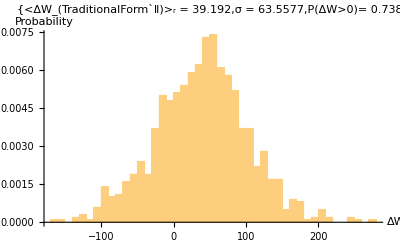

```mathematica
Histogram[N[WA⟦All,1⟧]-100,{10},PDF,AxesLabel->{"ΔW",Probability},PlotLabel->{ "<ΔW_(TraditionalForm`:2161)>_r = "<>ToString[WAM],"σ = "<>ToString[WAσ],"P(ΔW>0)= "<>ToString[WAP]},LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```

```mathematica
Ep=1000;
WAM=Mean[N[WA⟦All,2⟧-100,3]]
WAσ=StandardDeviation[N[WA⟦All,2⟧-100,4]]
WAP=N[1/Ep Total[UnitStep[N[WA⟦All,2⟧-100]]]]
```

68.597

1135.4

0.48

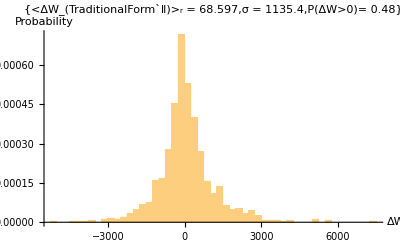

```mathematica
Histogram[N[WA⟦All,2⟧]-100,{250},PDF,AxesLabel->{"ΔW",Probability},PlotLabel->{ "<ΔW_(TraditionalForm`:2161)>_r = "<>ToString[WAM],"σ = "<>ToString[WAσ],"P(ΔW>0)= "<>ToString[WAP]},LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```

```mathematica
WA=Uncompress[ReadList["C:\\Users\\Jack\\Desktop\\LabWork\\final\\openm6s2T1279PRICE300REAL3000.txt",String]⟦1⟧]
```

{1}
 |  |  |  |

```mathematica
Dimensions[WA]
```

{3000,4}

```mathematica
Ep=3000;
WAM=Mean[N[WA⟦All,3⟧-3000,3]]
WAσ=StandardDeviation[N[WA⟦All,3⟧-3000,4]]
WAP=N[1/Ep Total[UnitStep[N[WA⟦All,3⟧-3000]]],3]
```

86.

174.

0.627

```mathematica
Ⅲ
```

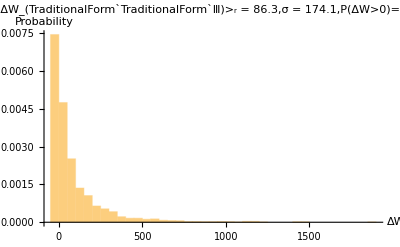

```mathematica
Histogram[N[WA⟦All,3⟧]-3000,{50},PDF,AxesLabel->{"ΔW",Probability},PlotLabel->{ "<ΔW_(TraditionalForm`TraditionalForm`:2162)>_r = "<>ToString[WAM],"σ = "<>ToString[WAσ],"P(ΔW>0)= "<>ToString[WAP]},LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```

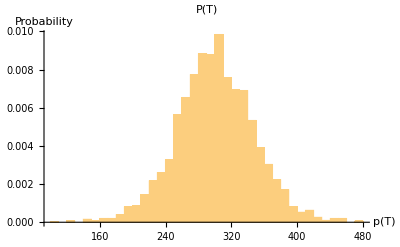

```mathematica
Histogram[N[WA⟦All,4⟧],{10},PDF,AxesLabel->{"p(T)",Probability},PlotLabel->"P(T)",LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```

```mathematica
N[Abs[(WA⟦All,4⟧-300)⟦1⟧]]
```

17.1146

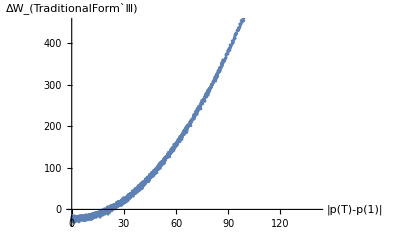

```mathematica
ListPlot[Table[N[{Abs[(WA⟦All,4⟧-300)⟦i⟧],(WA⟦All,3⟧-3000)⟦i⟧}],{i,1,3000}],AxesLabel->{"|p(T)-p(1)|","ΔW_(TraditionalForm`:2162)"},LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```